```mathematica
c=299792458
mAl=26.98153841
mCl35=34.96885269
mCl37=36.96590258
```

299792458

26.9815

34.9689

36.9659

```mathematica
mu35 = mCl35*mAl/(mAl+mCl35)
mu37 = mCl37*mAl/(mAl+mCl37)
```

15.2301

15.5971

```mathematica
eng[T_,we_,wexe_,v_,Be_,J_]:=T+we*(v+1/2)-wexe*(v+1/2)+Be*J*(J+1)
line[TA_,weA_,wexeA_,BeA_,JA_,weX_,wexeX_,BeX_,JX_,v_]:=eng[TA,weA,wexeA,v,BeA,JA]-eng[0,weX,wexeX,v,BeX,JX]
```

```mathematica
Solve[
{
line[TA,weA,wexeA,BeA,0,weX,wexeX,BeX,0,0]==f035,
line[TA,Sqrt[αw]*weA,wexeA,BeA,0,Sqrt[αw]*weX,wexeX,BeX,0,0]==f037
},{TA,weA}]//FullSimplify
```

{{TA→f035+(wexeA-wexeX)/2+(f035-f037)/(-1+√αw),weA→weX-(2 (f035-f037))/(-1+√αw)}}

```mathematica
Solve[
{
line[TA,weA,wexeA,BeA,0,weX,wexeX,BeX,0,1]==g035,
line[TA,Sqrt[αw]*weA,wexeA,BeA,0,Sqrt[αw]*weX,wexeX,BeX,0,1]==g037
},{TA,weA}]//FullSimplify
```

{{TA→g035+(3 (wexeA-wexeX))/2+(g035-g037)/(-1+√αw),weA→weX+(2 g035-2 g037)/(3-3 √αw)}}

```mathematica
Solve[
{
line[TA,weA,wexeA,BeA,0,weX,wexeX,BeX,0,0]==f035,
line[TA,Sqrt[αw]*weA,wexeA,BeA,0,Sqrt[αw]*weX,wexeX,BeX,0,0]==f037,
line[TA,weA,wexeA,BeA,0,weX,wexeX,BeX,0,1]==g035
},{TA,weA,wexeA}]//FullSimplify
```

{{TA→1/2 (3 f035-g035),weA→weX-(2 (f035-f037))/(-1+√αw),wexeA→f035-g035+wexeX-(2 (f035-f037))/(-1+√αw)}}

## Fitting least squares of data

```mathematica
os=1146.330906*10^12;

os1 = 1145.243625*10^12- os;

UX10=1880.20433;
UX20=-32.01271;
UX30=3.95499*10^-2;

offsetX35[v_]:= 100*c*(UX10/Sqrt[mu35]*(v+1/2)+UX20/Sqrt[mu35]^2*(v+1/2)^2+UX30/Sqrt[mu35]^3*(v+1/2)^3); 
offsetX37[v_]:= 100*c*(UX10/Sqrt[mu37]*(v+1/2) +UX20/Sqrt[mu37]^2*(v+1/2)^2+UX30/Sqrt[mu35]^3*(v+1/2)^3);
```

```mathematica
(* 35/37,freq,vA,JA,vX,JX *)
dataset = {
{35,0.1,0,1,0,1},
{37,6.27,0,1,0,1},
{35,14.5618,0,1,0,0},
{37,20.4348,0,1,0,0},
{35,29.1182,0,2,0,1},
{37,34.7858,0,2,0,1},
{35,43.8723,0,3,0,2},
{37,49.0800,0,3,0,2},
{35,58.7524,0,4,0,3},
{37,63.4467,0,4,0,3},
{35,73.6029,0,5,0,4},
{37,78.0327,0,5,0,4},
{35,88.6923,0,6,0,5},
{37,92.5861,0,6,0,5},


{35,-29.0887,0,1,0,2},

{35,-43.7385,0,2,0,3},
{37,-36.5956,0,2,0,3},
{35,-58.0894,0,3,0,4},
{37,-50.6758,0,3,0,4},
{35,-72.5155,0,4,0,5},
{37,-64.5582,0,4,0,5},
{35,-86.7899,0,5,0,6},
{37,-78.6428,0,5,0,6},
{35,-101.064,0,6,0,7},
{37,-92.280,0,6,0,7},

(* 1 -> 1 transition *)

{35,os1/10^9+0.0412,1,1,1,1},
{37,os1/10^9+21.6791,1,1,1,1},


{35,os1/10^9+14.7,1,1,1,0},
{35,os1/10^9+29.1,1,2,1,1},
{35,os1/10^9+43.55,1,3,1,2}


};
```

```mathematica
ordern = 2;
orderl = 2;

linevec[vA_,JA_,vX_, JX_, αwe_, αBe_]:=Flatten[
{
Table[αwe^(n)*(vA+1/2)^n,{n,0,ordern}],
Table[(JA*(1+JA)*αBe)^l,{l,1,orderl}],
JA*(1+JA)*αBe*(vA+1/2)*αwe,
(*-Table[αwe^n*(vX+1/2)^n,{n,1,ordern}],*)
-Table[(JX*(1+JX)*αBe)^l,{l,1,orderl}],
-JX*(1+JX)*αBe*(vX+1/2)*αwe
}]

Yvec = Flatten[
{
Table[YA[k, 0],{k,0,ordern}],
Table[YA[0, l],{l,1,orderl}],
YA[1,1],
(*Table[YX[k, 0],{k,1,ordern}],*)
Table[YX[0, l],{l,1,orderl}],
YX[1,1]
}
]

linevec[vA,JA,vX,JX,αwe,αBe].Yvec
```

{YA[0,0],YA[1,0],YA[2,0],YA[0,1],YA[0,2],YA[1,1],YX[0,1],YX[0,2],YX[1,1]}

YA[0,0]+JA (1+JA) αBe YA[0,1]+JA^2 (1+JA)^2 αBe^2 YA[0,2]+(1/2+vA) αwe YA[1,0]+JA (1+JA) (1/2+vA) αBe αwe YA[1,1]+(1/2+vA)^2 αwe^2 YA[2,0]-JX (1+JX) αBe YX[0,1]-JX^2 (1+JX)^2 αBe^2 YX[0,2]-JX (1+JX) (1/2+vX) αBe αwe YX[1,1]

```mathematica
model=Table[
If[dataset[[k,1]]==35,
linevec[dataset[[k,3]],dataset[[k,4]],dataset[[k,5]],dataset[[k,6]],1,1],
linevec[dataset[[k,3]],dataset[[k,4]],dataset[[k,5]],dataset[[k,6]],Sqrt[mu35/mu37],(mu35/mu37)]
]
,{k,1,Length[dataset]}];

rawdata=Table[
If[dataset[[k,1]]==35,
os+10^9*dataset[[k,2]]+offsetX35[dataset[[k,5]]],
os+10^9*dataset[[k,2]]+offsetX37[dataset[[k,5]]]
]
,{k,1,Length[dataset]}
];
```

```mathematica
sol=LeastSquares[model,rawdata];
residuals=model.sol-rawdata;

MresultA=0*IdentityMatrix[orderl*ordern];
MresultX=0*IdentityMatrix[orderl*ordern];

For[k=1,k≤Length[sol],k+=1,
n=Yvec[[k]][[1]];
l=Yvec[[k]][[2]];
hlp=sol[[k]]/100/c *(mu35)^(n/2+l);
Print["U",Yvec[[k]]," = ",NumberForm[hlp,10]];

If[k≤1+ordern+orderl+1,
MresultA[[n+1,l+1]]=hlp,
MresultX[[n+1,l+1]]=hlp
]
]

MresultX[[2,1]]=UX10;
MresultX[[3,1]]=UX20;
MresultX[[4,1]]=UX30;

Print["Residuals"]
Print[residuals/10^6  MHz]
Print["Total residuals = ", Total[Abs[residuals/10^9]] GHz]
```

UYA[0,0] = 38253.57064

UYA[1,0] = 1759.97464

UYA[2,0] = -73.48567729

UYA[0,1] = 3.749573251

UYA[0,2] = 0.002206966113

UYA[1,1] = -0.2959988247

UYX[0,1] = 3.743392824

UYX[0,2] = -0.0001736787064

UYX[1,1] = -0.3048405137

Residuals

{13.0677 MHz,-212.281 MHz,134.521 MHz,-135.183 MHz,228.264 MHz,-179.287 MHz,175.404 MHz,-117.26 MHz,69.256 MHz,-57.7923 MHz,94.4197 MHz,-120.033 MHz,18.7781 MHz,-17.3915 MHz,35.7995 MHz,171.39 MHz,-4.80713 MHz,61.8718 MHz,-47.5522 MHz,104.037 MHz,-214.561 MHz,101.062 MHz,-77.1551 MHz,241.808 MHz,-249.216 MHz,432.407 MHz,-489.013 MHz,49.3451 MHz,9.81044 MHz,-19.7073 MHz}

Total residuals = 3.88248 GHz

```mathematica
StringReplace[ExportString[NumberForm[MresultX,10],"String","FieldSeparators"->"["],{"{"->"[","}"->"]"}]
StringReplace[ExportString[NumberForm[MresultA,10],"String","FieldSeparators"->"["],{"{"->"[","}"->"]"}]
```

[[0, 3.697689639, -0.00004110220051, 0, 0, 0], [1880.20433, 0.04887253993, 0, 0, 0, 0], [-32.01271, 0, 0, 0, 0, 0], [0.0395499, 0, 0, 0, 0, 0], [0, 0, 0, 0, 0, 0], [0, 0, 0, 0, 0, 0]]

[[38255.63489, 3.718219212, 0.00273806453, 0, 0, 0], [1729.598167, -0.06421374131, 0, 0, 0, 0], [60.74391688, 0, 0, 0, 0, 0], [-180.1417929, 0, 0, 0, 0, 0], [0, 0, 0, 0, 0, 0], [0, 0, 0, 0, 0, 0]]

```mathematica
(*Q00*)
NumberForm[rawdata[[1]]/10^12-offsetX35[0]/10^12,10]
NumberForm[rawdata[[2]]/10^12-offsetX35[0]/10^12,10]

(*Q11*)
NumberForm[rawdata[[Length[rawdata]-1]]/10^12-offsetX35[1]/10^12,10]
NumberForm[rawdata[[Length[rawdata]]]/10^12-offsetX37[1]/10^12,10]
```

1146.331006

1146.252079

1145.272725

1145.540242

```mathematica
NumberForm[(model.sol)[[Length[rawdata]]]/10^12-offsetX37[1]/10^12,10]
```

1145.265014

```mathematica
linevec[vA,JA,vX,JX,αwe,αBe]
```

{1,(1/2+vA) αwe,(1/2+vA)^2 αwe^2,JA (1+JA) αBe,JA^2 (1+JA)^2 αBe^2,JA (1+JA) (1/2+vA) αBe αwe,-JX (1+JX) αBe,-JX^2 (1+JX)^2 αBe^2,-JX (1+JX) (1/2+vX) αBe αwe}

```mathematica
NumberForm[(linevec[0,1,0, 1, 1, 1].sol)/10^12-offsetX35[0]/10^12,10]
NumberForm[(linevec[0,1,0, 1, Sqrt[mu35/mu37], mu35/mu37].sol)/10^12-offsetX37[0]/10^12,10]

NumberForm[(linevec[1,1,1, 1, 1, 1].sol)/10^12-offsetX35[1]/10^12,10]
NumberForm[(linevec[1,1,1, 1, Sqrt[mu35/mu37], mu35/mu37].sol)/10^12-offsetX37[1]/10^12,10]
```

1146.331011

1146.336974

1145.244145

1145.26481

## Plot Morse Potentials

```mathematica
amorse[ke_,De_]:= Sqrt[ke/(2De)]
Morse[r_,re_,ke_,De_]:=De*(1-Exp[-amorse[ke,De]*(r-re)])^2

h = 6.62607*10^-34;
c = 299792458;
amu = 1.660539*10^-27;
echarge=1.602176*10^-19;

Bconst[Inert_]:=1/(2π) * hc/(4π*Inert) (* in linear frequency *)
weconst[ke_,μ_]:=1/(2π) * Sqrt[ke/μ] (* in linear frequency *)

Inert[m1_,m2_,re_]:=(m1*m2)/(m1+m2)*re^2
```

```mathematica
Bconst[Inert[mAl,mCl35,2.1366*10^-10]*amu]/c/100/.hc->h
```

0.242463

```mathematica
Solve[Bconst[Inert[m1,m2,Re]]==Be,Re]
```

{{Re→-(√hc √(m1+m2))/(2 √2 √Be √m1 √m2 π)},{Re→(√hc √(m1+m2))/(2 √2 √Be √m1 √m2 π)}}

```mathematica
(((h we^2)/(4 wexe)-h*we/2)/echarge-24223*100*c*h/echarge)/.we->527*100*c/.wexe->(2.652*100*c)
```

0.210102

```mathematica
Solve[
{
2π*we==Sqrt[ke/μ],
hc*wexe==hc^2*we^2/(4*De)
},
{De,ke}]
```

{{De→(hc we^2)/(4 wexe),ke→4 π^2 we^2 μ}}

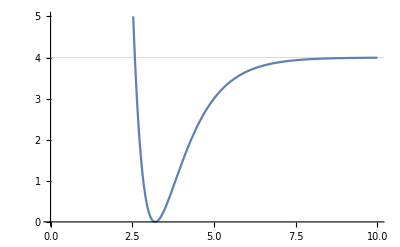

```mathematica
Plot[
Morse[r,3.2,10,4],{r,0,10},GridLines->{{},{4}},PlotRange->{0,5}]
```

```mathematica
3.710086911/mu35
3.703932569/mu35
```

0.243602

0.243197

```mathematica
With[
{
ABe=100*c*3.710086911/mu35,
XBe=100*c*3.703932569/(mu35),
hc = h,
m1=massAl * amu,
m2=massCl35 * amu,
Xwe=100*c*1880.20433/Sqrt[mu35],
Awe=100*c*1736.170635/Sqrt[mu35]
},
XRe=(√hc √(m1+m2))/(2 √2 √Be √m1 √m2 π)/10^-10/.Be->XBe;
ARe=(√hc √(m1+m2))/(2 √2 √Be √m1 √m2 π)/10^-10/.Be->ABe;

Xke=4 π^2 we^2 (m1*m2)/(m1+m2)/.we->Xwe;
Ake=4 π^2 we^2 (m1*m2)/(m1+m2)/.we->Awe;

XDe=(hc we^2)/(4 wexe)/.we->Xwe;
ADe=(hc we^2)/(4 wexe)/.we->Awe;

Print["X-State\nRe=",XRe," A\nke=", Xke, "N/m\nXDe=", XDe];
Print["A-State\nRe=",ARe," A\nke=", Ake, "N/m\nADe=", ADe];
]
```

X-State
Re=2.13337 A
ke=208.286N/m
XDe=(3.45576×10^-8)/wexe

A-State
Re=2.1316 A
ke=177.597N/m
ADe=(2.94658×10^-8)/wexe